```mathematica
SetDirectory[NotebookDirectory[]];
```

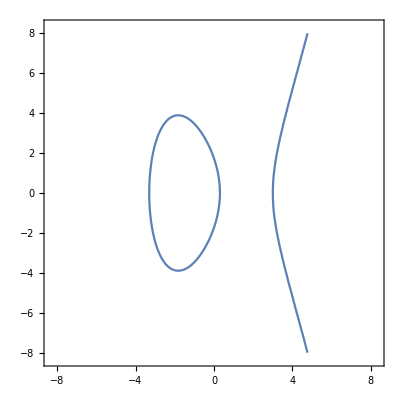

```mathematica
name="eliptic";
ContourPlot[y^2==x^3-10x+3,{x,-8,8},{y,-8,8}]
Export[{name<>".pdf",name<>".svg"},%];
```

```mathematica
y^2==x^3-10x+3/.{x->3,y->0}
y^2==x^3-10x+3/.{x->0,y->Sqrt[3]}
y^2==x^3-10x+3/.{x->1,y->Sqrt[2]}
```

True

True

False

```mathematica
Solve[x^3-10x+3==Sqrt[2]]
```

{{x→Root-3.24Root[{-2+#1^2&,3-#1-10 #2+#2^3&},{2,1}]-3.238769249057441},{x→Root0.159Root[{-2+#1^2&,3-#1-10 #2+#2^3&},{2,2}]0.15898046351029677},{x→Root3.08Root[{-2+#1^2&,3-#1-10 #2+#2^3&},{2,3}]3.079788785547144}}